## Annihilations

```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
Install["Suave-Linux"];
Install["Vegas-Linux"];
Install["Divonne-Linux"];
```

```mathematica
tempConversion = (1*^-9/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
hBar = 1.054571800*^-34;


vAvg[mx_, temp_] := (6*temp*tempConversion)/mx;

capRate = 1.*^22*6.58*^-16*1*^-9; (*test cap rate*)
```

## "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "===", "

```mathematica
(*================================================================================================================================================================*)

(* s = scalar, p = psedoscalar, v = vector, a = axialvector *)

ssME[q_, dmm_] := 16*NM^2*dmm^2;

psME[q_, dmm_] := 4*NM^2*q^2;

pspsME[q_, dmm_] := q^4;
```

## RowBox[{"q_", ",", " ", "q0_"}], "]"}], " ", ":=", " ", FractionBox[ RowBox[{ SuperscriptBox["NM", "2"], "*", "q0"}], RowBox[{"Pi", "*", "q"}]]}], ";"}], "\[IndentingNewLine]", RowBox[{ RowBox[{ RowBox[{ RowBox[{"denomInt", "[",

```mathematica
responseFn[q_, q0_] := (NM^2*q0)/(Pi*q);
denomInt[ki_, ME_, dmm_] :=Module[
{q, q0, cos},
q = √(ki^2+kp^2- 2* ki*kp*cos);
q0 = 1/(2*dmm)*(ki^2- kp^2);
 Integrate[(ME[q, dmm]*q0)/(16*NM^2*dmm^2*(2*π)^2)*kp^2*responseFn[q, q0],{kp, 0, ki}, {cos, -1, 1}, Assumptions->{ki>kp, kp>0}]
];

gSqr[ME_, dmm_, temp_] := Module[(*coupling constant squared in Natural units*)
{k0, kn,T},
T = temp*tempConversion;
k0 = dmm/3;
kn = Sqrt[3*T*dmm];
-1/TT*Integrate[ki/(dmm*denomInt[ki, ME, dmm]), {ki, k0, kn}, Assumptions->{k0>kn, kn>0}]
];
```

## data", "Subsubsection", CellChangeTimes->{{3.773719162886909*^9, 3.773719162888196*^9}, 3.773875317535226*^9, 3.7738910774351015`*^9}, ExpressionUUID -> "c4d82307-018e-4c03-bcf2-880bc43a7487"], Cell[CellGroupData[{ Cell[BoxData[{ RowBox[{ RowBox[{"EoSHeaders", " ", "=", " ", RowBox[

#### 24_lowmass.dat\>\"", "]"}]}], ";"}], "\[IndentingNewLine]", RowBox[{ RowBox[{"Dataset", "[", RowBox[{"EoSHeaders", "[", RowBox[{"[", RowBox[{"1", ",", "All"}], "]"}], "]"}], "]"}], " ", R

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

"\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"rMin", " ", "=", " ", 
   RowBox[{"radius", "[", 
    RowBox[{"[", "1", "]"}], "]"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{
   RowBox[{"rMax", " ",

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)
muFe     = Interpolation[ EoSData[[All, {1,10}]] ]; (* Chemical potential in MeV *)
muFμ     = Interpolation[ EoSData[[All, {1,11}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

(*ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)*)

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 
(*================================================================================================================================================================*)
potentialInside[rad_?NumericQ] := Which[rad ≤10.^-6, 0, True, NIntegrate[(NSMass[r])/r^2, {r, rMin, rad}]*(G*2.*^30)/(1.*^3*SOL^2)];
pot = Interpolation[Table[potentialInside[x], {x, 0, rMax}]];
(*================================================================================================================================================================*)
```

## " ", "0", ",", "0", ",", "0"}], "}"}], "*", "1.*^-3"}]}], ";"}], RowBox[{"(*", " ", RowBox[{"{", RowBox[{"e", ",", " ", "\[Mu]", ",", " ", "\[Tau]", ",", SubscriptBox["\[Nu]", "e"], ",", " ",

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *)
```

```mathematica
fT = {Mean[{0.019, 0.022, 0.012, 0.011, 0.014, 0.018}], Mean[{0.041, 0.049, 0.033, 0.027, 0.036, 0.042}], Mean[{0.14, 0.36, 0.053, 0.045, 0.118, 0.26}]}

fTG = 1. - Sum[fT[[n]], {n, 1, 3}];

DeltaN = {Mean[{-0.4, -0.43, -0.44, -0.43, -0.48, -0.43}],Mean[{0.77, 0.86, 0.84, 0.84, 0.78, 0.84}], Mean[{-0.12, -0.09, -0.03, -0.085, -0.15, -0.08}]}

deltaN = { 0.23,-0.84, 0.05}(* {u, d, s} *)
```

{0.016,0.038,0.162667}

{-0.435,0.821667,-0.0925}

{0.23,-0.84,0.05}

```mathematica
c12 = Sum[(NM*fT[[n]])/quarkMasses[[n]],{n, 1,3}] +(2.*fTG)/27.*(Sum[NM/quarkMasses[[n]], {n, 3, 6}] - NM);
mBar = 1./Sum[1./quarkMasses[[n]], {n, 1, 3}];
C34 = Sum[mBar/quarkMasses[[n]],{n,1,6}];
c34 = Sum[NM/quarkMasses[[n]]*(1 - C34 +mBar)*DeltaN[[n]],{n, 1,3}];
c56 = 3.;
c78 = Sum[DeltaN[[n]], {n, 1, 3}];
c910 = Sum[deltaN[[n]], {n, 1, 3}];
```

## RowBox[{ RowBox[{ RowBox[{"-", RowBox[{"muF\[Mu]", "[", "r", "]"}]}], "*",

```mathematica
fde[r_, mx_]:=HeavisideTheta[-muFe[r]*1*^-3 +mx];
fdμ[r_, mx_]:=HeavisideTheta[-muFμ[r]*1*^-3 +mx];
fdoth[r_, mx_] := 1.;
fdSelect[mf_]:= Which[mf == lepMasses[[1]], fde, mf == lepMasses[[2]], fdμ, True, fdoth];
```

```mathematica
fdSelect[lepMasses[[3]]][1,1]
```

1.

## RowBox[{"3", "/", "2"}]], "*", RowBox[{"vAvg", "[", RowBox[{"mx", ",", " ", "temp"}], "]"}]}], ",", " ", RowBox[{"{", RowBox[{"mf", ",", " ", RowBox[{"Select", "[", RowBox[{"quark

```mathematica
ssACS[r_, mx_, temp_] :=(Sum[(mx^2/(16.*π))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp]*fdSelect[mf][r, mx], {mf, Select[lepMasses, #≤ mx&]}]+Sum[((3.*mx^2)/(16.*π))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)

ppACS[r_,mx_, temp_] :=(Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx](**(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2](**(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

vvACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2 Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)


aaACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

ttACS[r_,mx_, temp_] := (Sum[(1./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][r, mx]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π))*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);
```

## 126639*^9, 3.775452127858129*^9}, {3.775453511497287*^9, 3.775453511783497*^9}, {3.7754688122937384`*^9, 3.7754688125536804`*^9}, { 3.775468979172984*^9,

75468986779807*^9}, {3.7754692264986753`*^9, 
   3.775469230644128*^9}},
 ExpressionUUID -> "63fd2475-13da-4abb-8500-af2266979922"],

Cell["General density profile", "Text",
 CellChangeTime

```mathematica
{{3.775438377730577*^9, 
  3.7754383888993797`*^9}},ExpressionUUID->"53719f37-6d9f-4ac4-9dc0-\
42d26a438c1e"],

Cell[BoxData[
 RowBox[{
  RowBox[{
   RowBox[{"ndFac", "[", 
    RowBox[{
     RowBox[{"mx_", "?", "NumericQ"}], ",", " ", 
     RowBox[{"temp_", "?", "NumericQ"}]}], "]"}], " ", ":=", 
   FractionBox[
    RowBox[{"NIntegrate", "[", 
     RowBox[{
      RowBox[{
       RowBox[{"Exp", "[", 
        FractionBox[
         RowBox[{
          RowBox[{"-", "2."}], "*", "mx", "*", 
          RowBox[{"potentialInside", "[", "rad", "]"}]}], "temp"], "]"}], "*", 
       RowBox[{"rad", "^", "2"}]}], ",", " ", 
      RowBox[{"{", 
       RowBox[{"rad", ",", " ", "rMin", ",", " ", "rMax"}], "}"}]}], "]"}], 
    RowBox[{"4.", "*", "Pi", "*", 
     SuperscriptBox[
      RowBox[{"(", 
       RowBox[{"NIntegrate", "[", 
        RowBox[{
         RowBox[{
          RowBox[{"Exp", "[", 
           FractionBox[
            RowBox[{
             RowBox[{"-", "mx"}], "*", 
             RowBox[{"potentialInside", "[", "rad", "]"}]}], "temp"], "]"}], 
          "*", 
          RowBox[{"rad", "^", "2"}]}], ",", " ", 
         RowBox[{"{", 
          RowBox[{"rad", ",", " ", "rMin", ",", " ", "rMax"}], "}"}]}], "]"}],
        ")"}], "2"]}]]}], ";"}]], "Input",
 CellChangeTimes->{{3.775340653121046*^9, 3.775340672442622*^9}, {
   3.7753407318777647`*^9, 3.775340732427266*^9}, {3.7753407684084187`*^9, 
   3.775340832332477*^9}, {3.7753409669681873`*^9, 3.775341001076007*^9}, {
   3.775341056835657*^9, 3.775341073311718*^9}, {3.775341313707069*^9, 
   3.775341321685817*^9}, {3.775341387803726*^9, 3.775341413635412*^9}, 
   3.775341458300128*^9, {3.775341750761278*^9, 3.77534175156531*^9}, {
   3.7753418679265537`*^9, 3.775341907240881*^9}, {3.775342132918358*^9, 
   3.775342161757093*^9}, {3.775342345731702*^9, 3.775342383958955*^9}, {
   3.7753424228531446`*^9, 3.775342472477331*^9}, {3.775346611809038*^9, 
   3.77534671381493*^9}, {3.77534677501611*^9, 3.77534677667776*^9}, 
   3.775346900222818*^9, {3.77534693766404*^9, 3.7753469433503942`*^9}, {
   3.77534702289467*^9, 3.77534702405965*^9}, {3.775347323050379*^9, 
   3.7753473555407047`*^9}, {3.775347392043914*^9, 3.775347418525264*^9}, {
   3.7753624149624434`*^9, 3.775362476640329*^9}, {3.7754383341327477`*^9, 
   3.775438335051898*^9}, 3.775438390243795*^9, {3.775438561711701*^9, 
   3.775438577231285*^9}, {3.775438809848878*^9, 3.7754388146274977`*^9}, {
   3.775451896488915*^9, 3.7754519065365562`*^9}},
 ExpressionUUID -> "eecc701e-43ca-4960-bb7f-fec2a285f422"],

Cell["Testing finding thermal radius", "Text",
 CellChangeTimes->{{3.7754401378763638`*^9, 
  3.775440153061907*^9}},ExpressionUUID->"0126becc-4555-4a76-a491-\
f44d07c1cea2"],

Cell[CellGroupData[{

Cell[BoxData[
 RowBox[{"Show", "[", 
  RowBox[{
   RowBox[{"LogLogPlot", "[", 
    RowBox[{"rMin", ",", " ", 
     RowBox[{"{", 
      RowBox[{"x", ",", " ", "1*^-6", ",", " ", "1*^6"}], "}"}]}], "]"}], ",",
    "\[IndentingNewLine]", 
   RowBox[{"ListLogLogPlot", "[", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"With", "[", 
        RowBox[{
         RowBox[{"{", 
          RowBox[{"m", " ", ":=", 
           SuperscriptBox["10.", "mp"]}], "}"}], ",", 
         RowBox[{"Table", "[", 
          RowBox[{
           RowBox[{"{", 
            RowBo
```

"m", ",", " ", 
             RowBox[{"x", "/.", 
              RowBox[{"FindRoot", "[", 
               RowBox[{
                RowBox[{
                 RowBox[{"m"

```mathematica
*", 
                  RowBox[{"potentialInside", "[", "x", "]"}]}], " ", 
                 "\[Equal]", " ", 
                 RowBox[{
                  FractionBox["3.", "2"], "*", "8.62069", "*", 
                  SuperscriptBox["10", 
                   RowBox[{"-", "9"}]]}]}], ",", 
                RowBox[{"{", 
                 RowBox[{"x", ",", " ", "0.001"}], "}"}]}], "]"}]}]}], "}"}], 
           ",", " ", 
           RowBox[{"{", 
            RowBox[{"mp", ",", " ", 
             RowBox[{"-", "6"}], ",", " ", "6", ",", "1"}], "}"}]}], "]"}]}], 
        "]"}], ",", " ", 
       RowBox[{"With", "[", 
        RowBox[{
         RowBox[{"{", 
          RowBox[{"m", " ", ":=", 
           SuperscriptBox["10.", "mp"]}], "}"}], ",", 
         RowBox[{"Table", "[", 
          RowBox[{
           RowBox[{"{", 
            RowBox[{"m", ",", " ", 
             RowBox[{
              RowBox[{"rTh", "[", 
               RowBox[{"m", ",", 
                RowBox[{"10", "^", "5"}]}], "]"}], "/", "1*^3"}]}], 
            "\[IndentingNewLine]", "}"}], ",", " ", 
           RowBox[{"{", 
            RowBox[{"mp", ",", " ", 
             RowBox[{"-", "6"}], ",", " ", "6", ",", "1"}], "}"}]}], "]"}]}], 
        "]"}]}], "}"}], ",", " ", 
     RowBox[{"AxesLabel", "\[Rule]", 
      RowBox[{"{", 
       RowBox[{
       "\"\<\!\(\*SubscriptBox[\(m\), \(\[Chi]\)]\) [GeV]\>\"", ",", " ", 
        "\"\<\!\(\*SubscriptBox[\(r\), \(th\)]\) [km]\>\""}], "}"}]}], ",", 
     " ", 
     RowBox[{"PlotLegends", "\[Rule]", 
      RowBox[{"{", 
       RowBox[{"\"\<Numeric\>\"", ",", " ", "\"\<const density\>\""}], 
       "}"}]}]}], "]"}]}], "]"}]], "Input",
 CellChangeTimes->{{3.775440130614073*^9, 3.775440136137868*^9}, {
  3.775440201272304*^9, 3.775440348193541*^9}, {3.775440532293949*^9, 
  3.775440539924806*^9}, {3.7754521876514683`*^9, 3.775452215842206*^9}, {
  3.7754525718492804`*^9, 3.7754526726651697`*^9}, {3.775452741812902*^9, 
  3.7754529030034037`*^9}},
 ExpressionUUID -> "6e6e5a72-0e09-4b68-8bf1-e6ef5e771cc8"],

Cell[BoxData[
 TemplateBox[{GraphicsBox[{{{{{}, {}, {
         Directive[
          Opacity[1.], 
          RGBColor[0.368417, 0.506779, 0.709798], 
          AbsoluteThickness[1.6]], 
         LineBox[CompressedData["
1:eJxTTMoPSmViYGAwAWIQ/UV1SVvXQu0DB4+asfzqET1g94ejbJMYgt9+KTf1
VrcWnK+avn77uThNOL+c64PeNlcNON81aq2VopE6nC836dFOA3Y1OH/1DbE4
4w8qcL4L++HSWweV4fyIR68VWWcqwfkKZ4Q/K7Uowvlf5m42fxquAOf//LPE
ybReDs5nFL9jtzxSBqGfkVkpiVUKzl/OoeHPfFMc4d4HNslva0Xh/NsC3gvu
6QrD+TfjwtW3sQoi5H8u01obywvnXymYPWvXfw44/3d7/o1IFxY4X2lRzgU+
u//7Yfx3Kz+JM0/+BudrPsn/Zhr1Cs7P3X9N0mD2RTj/3845mjPPXrCH8f/P
4Pz/UuA1nH//y8qeV7bf4Pwnd/jrbNb9h/NbDU48tahkcYDxT5j3/Gg7zQHn
351XYOtczQvnT0zVKZ/5VgDO36O0XK1LSBjOv8Bv9N4wTRTOr7m/L/fzRHE4
X/B+NGvOG0k43+7gr6B/cjJwfonXgvJONzk4/xTj6lupfgpw/rLzbVcmpyrC
+eVbX0XJTlGC88+8u+ijvFcZzs+V3CVpdkkFzmeK0Spe8k8Vzn/cP3u5vLg6
nO8hPsFdXEsDzl+0jackK0QTIe/e
```

qSwvOn2cm3qjFpg3nQ/MLnA8AjUeX
Ng==
          "]]}}}, {}, {}}, {{}, {{{}, {
         Hue[0.67, 0.6, 0.6], 
         Directive[
          PointSize[0.012833333333333334`],

```mathematica
(*Show[LogLogPlot[rMin, {x, 1*^-6, 1*^6}],
ListLogLogPlot[{With[{m :=10.^mp},Table[{m, x/.FindRoot[m*potentialInside[x] == 3./2*8.62069*10^-9,{x, 0.001}]}, {mp, -6, 6,1}]], With[{m :=10.^mp},Table[{m, rTh[m,10^5]/1*^3
}, {mp, -6, 6,1}]]}, AxesLabel->{"m_χ [GeV]", "r_th [km]"}, PlotLegends->{"Numeric", "const density"}]]*)
```

InterpolatingFunction::dmval: Input value {6.66993×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

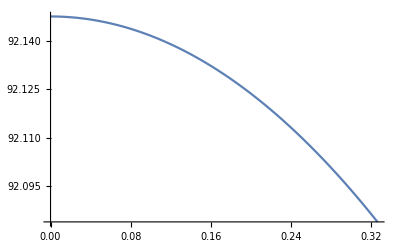

```mathematica
Plot[muFμ[x], {x, 0,rTh[0.0001, 1*^5]*1*^-3}]
```

## GridBoxSpacings -> { "Columns" -> {{0.5}}, "Rows" -> {{0.8}}}], "Grid"]}}, GridBoxAlignment -> {"Columns" -> {{Lef

```mathematica
anG[ACS_, mx_?NumericQ, temp_?NumericQ] :=1./((0.5*TT)^2*capRate*ndAnFac[mx, temp, ACS]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

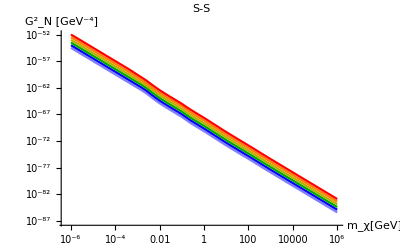

```mathematica
ssPlot = ListLogLogPlot[
 Evaluate@Table[
With[{x:=10^xp},
Table[{x,anG[ssACS, x, T]*c12^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
],

Joined->True, PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red},
AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"}, 
PlotLabel->"S-S", 
LabelStyle->Directive[Black,Bold]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

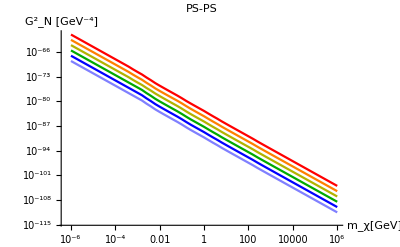

```mathematica
ppPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ppACS, x, T]*c34^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

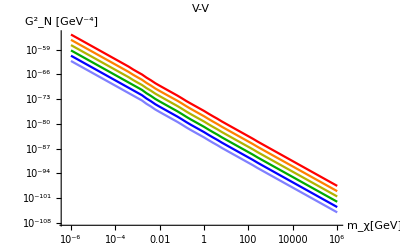

```mathematica
vvPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[vvACS, x, T]*c56^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"V-V", LabelStyle->Directive[Black,Bold]]
```

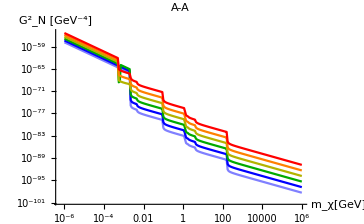

```mathematica
aaPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[aaACS, x, T]*c78^2},{xp, -6, 6, 0.05}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"A-A", LabelStyle->Directive[Black,Bold]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

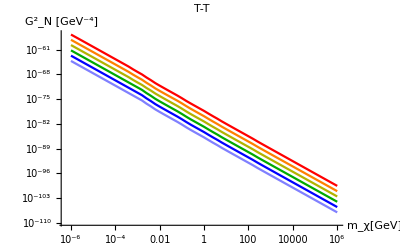

```mathematica
ttPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ttACS, x, T]*c910^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"T-T", LabelStyle->Directive[Black,Bold]]
```

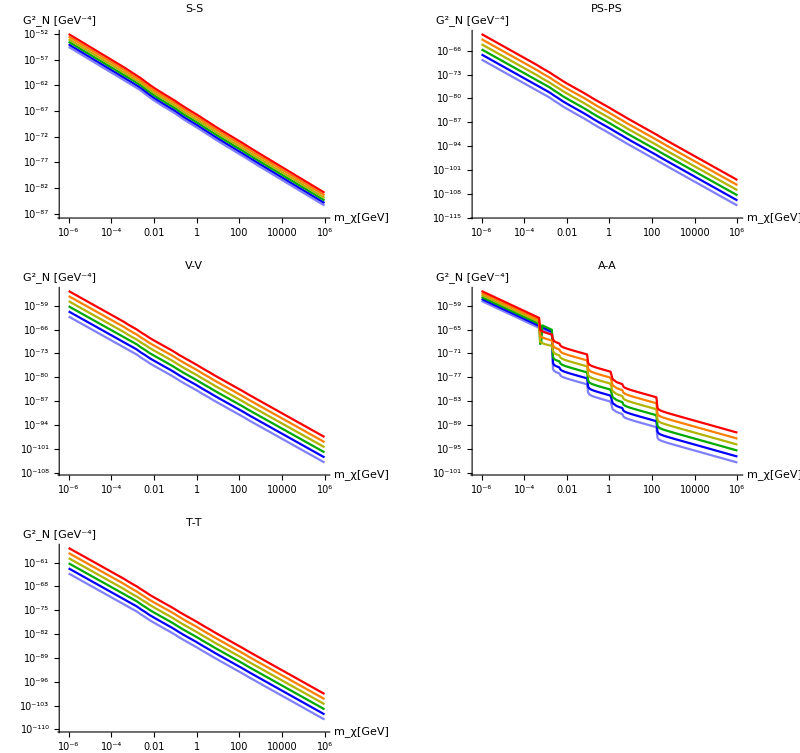

```mathematica
groupedPlots =Legended[GraphicsGrid[{{ssPlot, ppPlot}, {vvPlot, aaPlot}, {ttPlot}}, ImageSize->Full ], LineLegend[Reverse[{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}],Reverse[{"10^1K","10^2K","10^3K","10^4K", "10^5K", "10^6K"}]]]
```

```mathematica
Export["ann-limits.pdf", %]
```

ann-limits.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ann-limits.pdf"]]]
```